# Quantum Magnets + Impurity

This script employs exact diagonalization to compute the magnon spectrum and spin expectation values in various Quantum Magnets featuring a magnetic impurity (adatom) coupled to a single site. These materials are effectively modeled by the JKΓ extended Kitaev model.
	> we will focus mainly in two materials:  Subscript[RuCl, 3]  (e.g. 1706.06113 ) and Subscript[CrI, 3] (e.g. 1704.03849 )

## Preamble

```mathematica
Needs["MaTeX`"]

If[ FileNames@NotebookDirectory[]!=FileNames@Directory[],SetDirectory[NotebookDirectory[]] ];

Get[ FileNameJoin[{Directory[],"definitions.wl" }] ];

figFolder =FileNameJoin[{NotebookDirectory[],"Figures" }];
createDirectory@figFolder;
```

adatom_01

## Code

For small system sizes Lx,Ly < 3 on can run the code here, but the idea is to run it on the cluster
see “adatomLxLy.m” script files

## Figures

```mathematica
plotRange={-.77,-.55};
plotRangeS1={-.85,-.55};
plotRangeω={-.02,1.3};
```

### Kitaev FM (2,2)

#### code spin 1/2

Information/Parameters

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\adatom22\Kitaev_FM_size=(2,2)_2Simp=1\JK=Range[0,1,0.01]_k=100

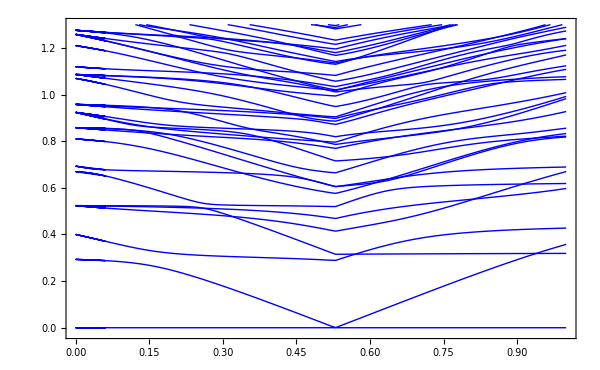

```mathematica
If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];
$FileName="adatom22.m";(*
Get[ FileNameJoin[{Directory[],"definitions.wl" }] ]*)
systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1/2};
gs               = {1};
KondoCouplings   = {0,1,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

	scriptName= StringReplace["adatomLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPath[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues22       =  dataRead[datapath];
	levels22          = Transpose@{#[[;;,1]],Lx Ly(#[[;;,2]]-#[[;;,2,1]])}&@eValues22;

	plotTitle  = StringReplace["\\text{Kitaev FM - } (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";
	
	figω22 = 
ListPlot[Transpose[Thread/@levels22],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->2]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->"Panel"],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},ImageSize->600,PlotRange->plotRangeω]    ]
```

#### code spin 1

```mathematica
If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];
$FileName="adatom22.m";(*
Get[ FileNameJoin[{Directory[],"definitions.wl" }] ]*)
systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1};
gs               = {1};
KondoCouplings   = {0,1,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

	scriptName= StringReplace["adatomLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPath[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues22s1      =  dataRead[datapath];
	levels22s1        = Transpose@{#[[;;,1]],Lx Ly(#[[;;,2]]-#[[;;,2,1]])}&@eValues22s1;

	plotTitle  = StringReplace["\\text{Kitaev FM - } (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "S_{\\text{imp}}=1, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";
	
	figω22s1 = 
ListPlot[Transpose[Thread/@levels22s1],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->2]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->"Panel"],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},ImageSize->600,PlotRange->plotRangeω]    ];
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\adatom22\Kitaev_FM_size=(2,2)_2Simp=2\JK=Range[0,1,0.01]_k=100

#### export

```mathematica
Column[  Show[#,ImageSize->500]&/@{figω22,figω22s1}  ]
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigOmega22.pdf" }],    figω22];
Export[     FileNameJoin[{ figFolder,"FigOmega22S1.pdf" }],    figω22s1];
```

### Kitaev FM (3,2)

#### code spin 1/2

Information/Parameters

```mathematica
If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];
$FileName="adatom32.m";
(*Get[ FileNameJoin[{Directory[],"definitions.wl" }] ]*)
systemDimensions = {{3,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1/2};
gs               = {1};
KondoCouplings   = {0,1,.05};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

scriptName= StringReplace["adatomLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPath[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues32       =  dataRead[datapath];
	levels32          = Transpose@{#[[;;,1]],Lx Ly(#[[;;,2]]-#[[;;,2,1]])}&@eValues32;

	plotTitle  = StringReplace["\\text{Kitaev FM - } (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";
	
	figω32 = 
ListPlot[Transpose[Thread/@levels32],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->2]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->"Panel"],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},ImageSize->600,PlotRange->plotRangeω ] ;
   ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\adatom32\Kitaev_FM_size=(3,2)_2Simp=1\JK=Range[0,1,0.05]_k=100

#### code spin 1

```mathematica
If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];
$FileName="adatom32.m";
(*Get[ FileNameJoin[{Directory[],"definitions.wl" }] ]*)
systemDimensions = {{3,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1};
gs               = {1};
KondoCouplings   = {0,1,.05};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

scriptName= StringReplace["adatomLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPath[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues32s1       =  dataRead[datapath];
	levels32s1          = Transpose@{#[[;;,1]],Lx Ly(#[[;;,2]]-#[[;;,2,1]])}&@eValues32s1;

	plotTitle  = StringReplace["\\text{Kitaev FM - } (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";

	figω32s1 = 
ListPlot[Transpose[Thread/@levels32s1],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->2]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->"Panel"],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},ImageSize->600,PlotRange->plotRangeω ] ;
   ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\adatom32\Kitaev_FM_size=(3,2)_2Simp=2\JK=Range[0,1,0.05]_k=100

#### export

```mathematica
Show[figEn32,ImageSize->500]
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigEn32.pdf" }],    figEn32];
```

```mathematica
Column[  Show[#,ImageSize->500]&/@{figω32,figω32s1}  ]
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigOmega32.pdf" }],    figω32];
Export[     FileNameJoin[{ figFolder,"FigOmega32S1.pdf" }],    figω32s1];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigOmega32.pdf" }],    figω32];
```

### Kitaev FM (3,3)

#### code - spin 1/2

Information/Parameters

```mathematica
If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];
(*Get[ FileNameJoin[{Directory[],"definitions.wl" }] ]*)
systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1/2};
gs               = {1};
KondoCouplings   = {0,1,.1};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 10;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;



Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};	scriptName= StringReplace["adatom_LX_LY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPath[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues33       =  Transpose@{#[[;;,1]],1/(Lx Ly)(#[[;;,2]])}&@dataRead[datapath][[1]];

	levels33          = Transpose@{#[[;;,1]],Lx Ly(#[[;;,2]]-#[[;;,2,1]])}&@eValues33;

	plotTitle  = StringReplace["\\text{Kitaev FM - } (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";

		figω33 = 
ListPlot[Transpose[Thread/@levels33],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->2]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->"Panel"],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},ImageSize->600,PlotRange->plotRangeω] ;
   ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\adatom_3_3\Kitaev_FM_size=(3,3)_2Simp=1\JK=Range[0,1,0.1]_k=10

#### code - spin 1

```mathematica
If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];
(*Get[ FileNameJoin[{Directory[],"definitions.wl" }] ]*)
systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1};
gs               = {1};
KondoCouplings   = {0,1,.05};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;



Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};	scriptName= StringReplace["adatomLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPath[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues33s1       =  Transpose@{#[[;;,1]],1/(Lx Ly)(#[[;;,2]])}&@dataRead[datapath];

	levels33s1         = Transpose@{#[[;;,1]],Lx Ly(#[[;;,2]]-#[[;;,2,1]])}&@eValues33s1;

	plotTitle  = StringReplace["\\text{Kitaev FM - } (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "S_{\\text{imp}}=1, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";

		figω33s1 = 
ListPlot[Transpose[Thread/@levels33s1],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->2]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->"Panel"],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},ImageSize->600,PlotRange->plotRangeω] ;
   ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\adatom33\Kitaev_FM_size=(3,3)_2Simp=2\JK=Range[0,1,0.05]_k=100

#### export

```mathematica
Column[Show[#,ImageSize->500]&/@{figω33,figω33s1  }]
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigOmega33.pdf" }],    figω33];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigOmega33S1.pdf" }],    figω33s1];
```

## Spin operators

Compute expectation values of spin operators. 
First take component along the c direction.

```mathematica
Ns=30;
JKmax=1;
dJK=JKmax/Ns;
For[i=0,i≤Ns,i++,
JK0=i dJK;
R=Chop[Eigensystem[N[H[JK0]]]];
sortR=SortBy[Table[{R[[1,i]],R[[2,i]]},{i,1,Length[H[JK0]]}],First];
Ψ[n_]:=sortR[[n,2]];
Mimp=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Id,Sum[cvec[[n]] Subscript[S, n],{n,1,3}]].Ψ[1];
Mbulk=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Sum[cvec[[n]] 1/2 Subscript[σ, n],{n,1,3}],IdS].Ψ[1];
Mimplist[i]=Chop[N[{JK0,Mimp}]];
Mbulklist[i]=Chop[N[{JK0,Mbulk}]]];
listMimp=Table[Mimplist[i],{i,0,Ns}];
listMbulk=Table[Mbulklist[i],{i,0,Ns}];
```

```mathematica
ListPlot[{listMimp,listMbulk},PlotStyle->{Blue,Red},Joined->False,Frame->True,PlotRange->All,FrameStyle->Directive[Black,16,Thickness[.002]],FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{c}}\\rangle"},ImageSize->450,PlotLegends->Placed[(MaTeX[#,Magnification->1.8]&)/@{"\\text{impurity}","\\text{bulk}"},{.8,.8}]]
```

Now the in-plane component along the a direction. 
This component is always zero for the impurity spin and the site to which it is coupled. 
Consider  j=3 as a neighboring site that shows the vortex-like pattern.

```mathematica
dJK=JKmax/Ns;
For[i=0,i≤Ns,i++,
JK0=i dJK;
R=Chop[Eigensystem[N[H[JK0]]]];
sortR=SortBy[Table[{R[[1,i]],R[[2,i]]},{i,1,Length[H[JK0]]}],First];
Ψ[n_]:=sortR[[n,2]];
Mimp=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Id,Sum[avec[[n]] Subscript[S, n],{n,1,3}]].Ψ[1];
Mneigh=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Sum[avec[[n]] 1/2 Subscript[σ, n],{n,1,3}],Id,Id,Id,Id,Id,IdS].Ψ[1];
Mimplist[i]=Chop[N[{JK0,Mimp}]];
Mneighlist[i]=Chop[N[{JK0,Mneigh}]]];
listMimp=Table[Mimplist[i],{i,0,Ns}];
listMneigh=Table[Mneighlist[i],{i,0,Ns}];
```

```mathematica
ListPlot[{listMimp,listMneigh},PlotStyle->{Blue,Magenta},Joined->False,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{a}}\\rangle"},ImageSize->450,PlotLegends->Placed[(MaTeX[#,Magnification->1.8]&)/@{"\\text{impurity}","\\text{bulk}, j=3"},{.8,.7}]]
```